{(-1+x) x,(-1+x) x^2,(-1+x) x^3,(-1+x) x^4,(-1+x) x^5,(-1+x) x^6}

{{0.39328,0.19664,0.135712,0.105248,0.0901972,0.0828531},{0.19664,0.168992,0.138528,0.118613,0.106405,0.0990774},{0.135712,0.138528,0.128085,0.118181,0.110757,0.1056},{0.105248,0.118613,0.118181,0.11465,0.110986,0.107953},{0.0901972,0.106405,0.110757,0.110986,0.10988,0.108471},{0.0828531,0.0990774,0.1056,0.107953,0.108471,0.10819}}

{-0.08,-0.04672,-0.03008,-0.020608,-0.01472,-0.0108268}

{-0.11044,-0.152526,-9.45126,43.0641,-66.0377,32.5888}

{{11/30,11/60,23/210,61/840,13/252,97/2520},{11/60,1/7,89/840,101/1260,157/2520,172/3465},{23/210,89/840,113/1260,187/2520,853/13860,17/330},{61/840,101/1260,187/2520,227/3465,113/1980,71/1430},{13/252,157/2520,853/13860,113/1980,133/2574,557/12012},{97/2520,172/3465,17/330,71/1430,557/12012,641/15015}}

{-1/12,-1/20,-1/30,-1/42,-1/56,-1/72}

{-191546527697/1284841384761,-1583036137/10618523841,-847653557/116803762251,-283443719/38934587417,-16569787/116803762251,-715/3724491}

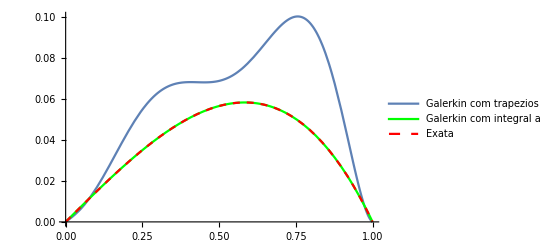

```mathematica
Tn[f_,a_,b_,m_]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[x^i*(x-1),{i,1,6}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,5],{j,6},{n,6}]
F=Table[Tn[x*ϕ[[j]]/.x->#&,0,1,5],{j,1,6}]
W=LinearSolve[K,F]
Uh[x_]:=W.ϕ
k=Table[Integrate[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]],{x,0,1}],{j,6},{n,6}]
f=Table[Integrate[x*ϕ[[j]],{x,0,1}],{j,1,6}]
w=LinearSolve[k,f]
uh[x_]:=w.ϕ

G1=Plot[{Uh[x],uh[x],x-Sinh[x]/Sinh[1]},{x,0,1},PlotStyle->{,Green,{Red,Dashed}},PlotLegends->{"Galerkin com trapezios compostos","Galerkin com integral analítica","Exata"},ImageSize->400,AxesStyle->Black]
```

```mathematica
Export["g1.png",G1]
```

g1.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["g1.png"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["g1.png"]]]
```

{(-1+x) x,(-1+x) x^2,(-1+x) x^3,(-1+x) x^4,(-1+x) x^5,(-1+x) x^6,(-1+x) x^7,(-1+x) x^8,(-1+x) x^9,(-1+x) x^10}

{{0.366733,0.183367,0.10959,0.0727024,0.0516873,0.0386087,0.0299313,0.0238873,0.0195139,0.0162505},{0.183367,0.142924,0.106036,0.0802587,0.0624182,0.0497726,0.040554,0.0336553,0.0283717,0.0242425},{0.10959,0.106036,0.0897825,0.074323,0.0616773,0.0516651,0.0437564,0.0374626,0.032401,0.0282843},{0.0727024,0.0802587,0.074323,0.0656456,0.0572207,0.049817,0.0435232,0.0382285,0.0337788,0.0300274},{0.0516873,0.0624182,0.0616773,0.0572207,0.0518372,0.0465536,0.041725,0.0374418,0.0336904,0.0304202},{0.0386087,0.0497726,0.0516651,0.049817,0.0465536,0.0428905,0.0392733,0.0358882,0.0328011,0.0300222},{0.0299313,0.040554,0.0437564,0.0435232,0.041725,0.0392733,0.0366208,0.0339916,0.0314928,0.0291702},{0.0238873,0.0336553,0.0374626,0.0382285,0.0374418,0.0358882,0.0339916,0.031983,0.0299872,0.02807},{0.0195139,0.0283717,0.032401,0.0337788,0.0336904,0.0328011,0.0314928,0.0299872,0.028414,0.0268485},{0.0162505,0.0242425,0.0282843,0.0300274,0.0304202,0.0300222,0.0291702,0.02807,0.0268485,0.0255837}}

{-0.083325,-0.0499917,-0.033325,-0.0238012,-0.0178488,-0.0138806,-0.0111028,-0.00908258,-0.00756743,-0.00640193}

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.366733,0.183367,0.10959,0.0727024,0.0516873,0.0386087,0.0299313,0.0238873,0.0195139,0.0162505},«8»,{0.0162505,0.0242425,0.0282843,0.0300274,0.0304202,0.0300222,0.0291702,0.02807,0.0268485,0.0255837}} may contain significant numerical errors.

{-0.143975,-0.286041,1.01723,-0.88268,-21.7595,114.301,-263.753,322.231,-202.953,51.9334}

{{11/30,11/60,23/210,61/840,13/252,97/2520,59/1980,47/1980,83/4290,193/12012},{11/60,1/7,89/840,101/1260,157/2520,172/3465,4/99,431/12870,1693/60060,361/15015},{23/210,89/840,113/1260,187/2520,853/13860,17/330,17/390,2239/60060,967/30030,613/21840},{61/840,101/1260,187/2520,227/3465,113/1980,71/1430,2603/60060,571/15015,733/21840,5531/185640},{13/252,157/2520,853/13860,113/1980,133/2574,557/12012,1247/30030,271/7280,6211/185640,517/17136},{97/2520,172/3465,17/330,71/1430,557/12012,641/15015,853/21840,6619/185640,2789/85680,173/5814},{59/1980,4/99,17/390,2603/60060,1247/30030,853/21840,193/5304,413/12240,3631/116280,3359/116280},{47/1980,431/12870,2239/60060,571/15015,271/7280,6619/185640,413/12240,461/14535,1727/58140,5651/203490},{83/4290,1693/60060,967/30030,733/21840,6211/185640,2789/85680,3631/116280,1727/58140,1907/67830,2329/87780},{193/12012,361/15015,613/21840,5531/185640,517/17136,173/5814,3359/116280,5651/203490,2329/87780,2549/100947}}

{-1/12,-1/20,-1/30,-1/42,-1/56,-1/72,-1/90,-1/110,-1/132,-1/156}

{-153406638324145908741405/1029009339045766393936601,-153406638325161953388085/1029009339045766393936601,-7472854849783359519310/1029009339045766393936601,-7472855075438696828110/1029009339045766393936601,-176164571261162672470/1029009339045766393936601,-176169435167891318806/1029009339045766393936601,-2427272525403134866/1029009339045766393936601,-2444934351873360466/1029009339045766393936601,-14571796761019666/1029009339045766393936601,-104006/4303299595211}

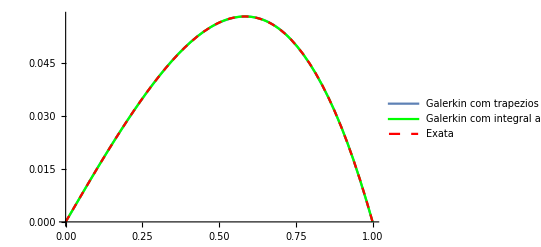

```mathematica
Tn[f_,a_,b_,m_]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[x^i*(x-1),{i,1,10}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,100],{j,10},{n,10}]
F=Table[Tn[x*ϕ[[j]]/.x->#&,0,1,100],{j,1,10}]
W=LinearSolve[K,F]
Uh[x_]:=W.ϕ
k=Table[Integrate[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]],{x,0,1}],{j,10},{n,10}]
f=Table[Integrate[x*ϕ[[j]],{x,0,1}],{j,1,10}]
w=LinearSolve[k,f]
uh[x_]:=w.ϕ

G2=Plot[{Uh[x],uh[x],x-Sinh[x]/Sinh[1]},{x,0,1},PlotStyle->{,Green,{Red,Dashed}},PlotLegends->{"Galerkin com trapezios compostos","Galerkin com integral analítica","Exata"},ImageSize->400,AxesStyle->Black]
```

```mathematica
Export["g2.png",G2]
```

g2.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["g2.png"]]]
```

{Sin[π x],Sin[2 π x],Sin[3 π x],Sin[4 π x],Sin[5 π x],Sin[6 π x]}

{{5.4348,-1.77636×10^-16,-7.10543×10^-16,0.,0.,0.},{-1.77636×10^-16,20.2392,0.,-2.84217×10^-15,0.,-2.84217×10^-15},{-7.10543×10^-16,0.,44.9132,0.,-5.68434×10^-15,-1.42109×10^-15},{0.,-2.84217×10^-15,0.,79.4568,0.,117.935},{0.,0.,-5.68434×10^-15,0.,246.74,0.},{0.,-2.84217×10^-15,-1.42109×10^-15,117.935,0.,178.153}}

{0.307768,-0.137638,0.0726543,-0.032492,0.,0.032492}

{0.0566292,-0.00680057,0.00161766,-0.0389904,3.72672×10^-20,0.0259936}

{{1/2 (1+π^2),0,0,0,0,0},{0,1/2+2 π^2,0,0,0,0},{0,0,1/2 (1+9 π^2),0,0,0},{0,0,0,1/2+8 π^2,0,0},{0,0,0,0,1/2 (1+25 π^2),0},{0,0,0,0,0,1/2+18 π^2}}

{1/π,-1/(2 π),1/(3 π),-1/(4 π),1/(5 π),-1/(6 π)}

{2/(π (1+π^2)),-1/(π (1+4 π^2)),2/(3 π (1+9 π^2)),-1/(2 π (1+16 π^2)),2/(5 π (1+25 π^2)),-1/(3 π (1+36 π^2))}

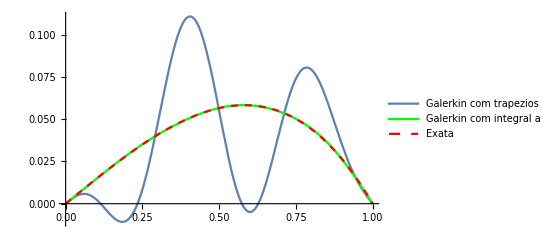

```mathematica
Tn[f_,a_,b_,m_]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[Sin[i*Pi*x],{i,1,6}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,5],{j,6},{n,6}]
F=Table[Tn[x*ϕ[[j]]/.x->#&,0,1,5],{j,1,6}]
W=LinearSolve[K,F]
Uh[x_]:=W.ϕ
k=Table[Integrate[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]],{x,0,1}],{j,6},{n,6}]
f=Table[Integrate[x*ϕ[[j]],{x,0,1}],{j,1,6}]
w=LinearSolve[k,f]
uh[x_]:=w.ϕ

G1=Plot[{Uh[x],uh[x],x-Sinh[x]/Sinh[1]},{x,0,1},PlotStyle->{,Green,{Red,Dashed}},PlotLegends->{"Galerkin com trapezios compostos","Galerkin com integral analítica","Exata"},ImageSize->400,AxesStyle->Black]
```

```mathematica
Export["g3.png",G1]
```

g3.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["g3.png"]]]
```

{Sin[π x],Sin[2 π x],Sin[3 π x],Sin[4 π x],Sin[5 π x],Sin[6 π x],Sin[7 π x],Sin[8 π x],Sin[9 π x],Sin[10 π x]}

{{5.4348,0.,0.,-4.44089×10^-17,-1.13687×10^-15,1.44329×10^-17,-1.7053×10^-15,-6.66134×10^-17,0.,7.10543×10^-17},{0.,20.2392,5.32907×10^-17,1.42109×10^-16,2.13163×10^-16,1.13687×10^-15,-4.44089×10^-17,1.06581×10^-16,1.06581×10^-16,0.},{0.,5.32907×10^-17,44.9132,5.77316×10^-17,-6.39488×10^-16,-4.26326×10^-16,-2.27374×10^-15,5.50671×10^-16,2.27374×10^-15,5.68434×10^-16},{-4.44089×10^-17,1.42109×10^-16,5.77316×10^-17,79.4568,9.59233×10^-16,-1.13687×10^-15,2.84217×10^-16,0.,-3.4639×10^-16,2.84217×10^-16},{-1.13687×10^-15,2.13163×10^-16,-6.39488×10^-16,9.59233×10^-16,123.87,-1.42109×10^-16,-2.84217×10^-15,-7.10543×10^-17,-1.13687×10^-15,-2.27374×10^-15},{1.44329×10^-17,1.13687×10^-15,-4.26326×10^-16,-1.13687×10^-15,-1.42109×10^-16,178.153,-3.10862×10^-16,0.,5.32907×10^-16,-4.54747×10^-15},{-1.7053×10^-15,-4.44089×10^-17,-2.27374×10^-15,2.84217×10^-16,-2.84217×10^-15,-3.10862×10^-16,242.305,1.16351×10^-15,-6.82121×10^-15,-1.13687×10^-15},{-6.66134×10^-17,1.06581×10^-16,5.50671×10^-16,0.,-7.10543×10^-17,0.,1.16351×10^-15,316.327,7.4607×10^-16,2.98428×10^-15},{0.,1.06581×10^-16,2.27374×10^-15,-3.4639×10^-16,-1.13687×10^-15,5.32907×10^-16,-6.82121×10^-15,7.4607×10^-16,400.219,-5.68434×10^-16},{7.10543×10^-17,0.,5.68434×10^-16,2.84217×10^-16,-2.27374×10^-15,-4.54747×10^-15,-1.13687×10^-15,2.98428×10^-15,-5.68434×10^-16,493.98}}

{0.318284,-0.159103,0.106025,-0.0794727,0.063531,-0.0528945,0.0452894,-0.0395791,0.0351318,-0.0315688}

{0.058564,-0.00786111,0.00236066,-0.0010002,0.000512884,-0.000296905,0.000186911,-0.000125121,0.0000877815,-0.0000639069}

{{1/2 (1+π^2),0,0,0,0,0,0,0,0,0},{0,1/2+2 π^2,0,0,0,0,0,0,0,0},{0,0,1/2 (1+9 π^2),0,0,0,0,0,0,0},{0,0,0,1/2+8 π^2,0,0,0,0,0,0},{0,0,0,0,1/2 (1+25 π^2),0,0,0,0,0},{0,0,0,0,0,1/2+18 π^2,0,0,0,0},{0,0,0,0,0,0,1/2 (1+49 π^2),0,0,0},{0,0,0,0,0,0,0,1/2+32 π^2,0,0},{0,0,0,0,0,0,0,0,1/2 (1+81 π^2),0},{0,0,0,0,0,0,0,0,0,1/2+50 π^2}}

{1/π,-1/(2 π),1/(3 π),-1/(4 π),1/(5 π),-1/(6 π),1/(7 π),-1/(8 π),1/(9 π),-1/(10 π)}

{2/(π (1+π^2)),-1/(π (1+4 π^2)),2/(3 π (1+9 π^2)),-1/(2 π (1+16 π^2)),2/(5 π (1+25 π^2)),-1/(3 π (1+36 π^2)),2/(7 π (1+49 π^2)),-1/(4 π (1+64 π^2)),2/(9 π (1+81 π^2)),-1/(5 π (1+100 π^2))}

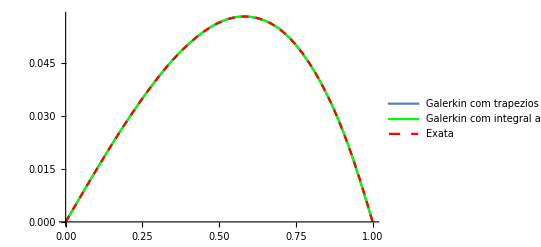

```mathematica
Tn[f_,a_,b_,m_]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[Sin[i*Pi*x],{i,1,10}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,100],{j,10},{n,10}]
F=Table[Tn[x*ϕ[[j]]/.x->#&,0,1,100],{j,1,10}]
W=LinearSolve[K,F]
Uh[x_]:=W.ϕ
k=Table[Integrate[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]],{x,0,1}],{j,10},{n,10}]
f=Table[Integrate[x*ϕ[[j]],{x,0,1}],{j,1,10}]
w=LinearSolve[k,f]
uh[x_]:=w.ϕ

G1=Plot[{Uh[x],uh[x],x-Sinh[x]/Sinh[1]},{x,0,1},PlotStyle->{,Green,{Red,Dashed}},PlotLegends->{"Galerkin com trapezios compostos","Galerkin com integral analítica","Exata"},ImageSize->400,AxesStyle->Black]
```

```mathematica
Export["s_n_10.png",G1]
```

s_n_10.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["s_n_10.png"]]]
```

```mathematica
Tn[f_,a_,b_,m_]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[x^i*(x-1),{i,1,6}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,5],{j,6},{n,6}]
F=Table[Tn[x*ϕ[[j]]/.x->#&,0,1,5],{j,1,6}]
W=LinearSolve[K,F]
Uh[x_]:=W.ϕ
k=Table[Integrate[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]],{x,0,1}],{j,6},{n,6}]
f=Table[Integrate[x*ϕ[[j]],{x,0,1}],{j,1,6}]
w=LinearSolve[k,f]
uh[x_]:=w.ϕ

G1=Plot[{Uh[x],uh[x],x-Sinh[x]/Sinh[1]},{x,0,1},PlotStyle->{,Green,{Red,Dashed}},PlotLegends->{"Galerkin com trapezios compostos","Galerkin com integral analítica","Exata"},ImageSize->400,AxesStyle->Black]
```

```mathematica
Tn[f_,a_,b_,m_]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[Sin[i*Pi*x],{i,1,6}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,5],{j,6},{n,6}]
F=Table[Tn[x*ϕ[[j]]/.x->#&,0,1,5],{j,1,6}]
W=LinearSolve[K,F]
k=Table[Integrate[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]],{x,0,1}],{j,6},{n,6}]
f=Table[Integrate[x*ϕ[[j]],{x,0,1}],{j,1,6}]
w=LinearSolve[k,f]
uh[x_]:=w.ϕ

Uh[x_]:=W.ϕ

G111=Plot[{Uh[x],uh[x],x-Sinh[x]/Sinh[1]},{x,0,1},PlotStyle->{,Green,{Red,Dashed}},PlotLegends->{"Galerkin com trapezios compostos","Galerkin com integral analítica","Exata"},ImageSize->400,AxesStyle->Black]
```

{Sin[π x],Sin[2 π x],Sin[3 π x],Sin[4 π x],Sin[5 π x],Sin[6 π x]}

{{5.4348,-1.77636×10^-16,-7.10543×10^-16,0.,0.,0.},{-1.77636×10^-16,20.2392,0.,-2.84217×10^-15,0.,-2.84217×10^-15},{-7.10543×10^-16,0.,44.9132,0.,-5.68434×10^-15,-1.42109×10^-15},{0.,-2.84217×10^-15,0.,79.4568,0.,117.935},{0.,0.,-5.68434×10^-15,0.,246.74,0.},{0.,-2.84217×10^-15,-1.42109×10^-15,117.935,0.,178.153}}

{0.307768,-0.137638,0.0726543,-0.032492,0.,0.032492}

{0.0566292,-0.00680057,0.00161766,-0.0389904,3.72672×10^-20,0.0259936}

{{1/2 (1+π^2),0,0,0,0,0},{0,1/2+2 π^2,0,0,0,0},{0,0,1/2 (1+9 π^2),0,0,0},{0,0,0,1/2+8 π^2,0,0},{0,0,0,0,1/2 (1+25 π^2),0},{0,0,0,0,0,1/2+18 π^2}}

{1/π,-1/(2 π),1/(3 π),-1/(4 π),1/(5 π),-1/(6 π)}

{2/(π (1+π^2)),-1/(π (1+4 π^2)),2/(3 π (1+9 π^2)),-1/(2 π (1+16 π^2)),2/(5 π (1+25 π^2)),-1/(3 π (1+36 π^2))}

-Graphics-